```mathematica
s[x_]:=Abs[x-Round[x]]
bmcr[x_,nmx_]:= Sum[s[2^n x]/2^n,{n,0,nmx}]
y[x_]:=-Sqrt[1/16-(x-1/4)^2]+1/2
```

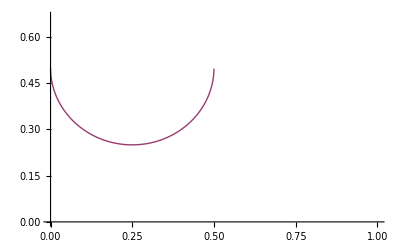

```mathematica
n=20;
Plot[{bmcr[x,n],y[x]},{x,0,1}]
```

```mathematica
(* Find intersection point! *)
rt=FindRoot[bmcr[x,30]-y[x],{x,0.2},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->20][[1,2]];
```

```mathematica
(* Approximate area uncer curve from x=rt to x=1/2*)
n = 27;
Timing[
sm=0;
xvlp=0;
i=0;
While[xvlp≤1/2,
{xvl,xvlp} = SetPrecision[{i/2^n,(i+1)/2^n},20];
{yvl,yvlp}={bmcr[xvl,n],bmcr[xvlp,n]};
If[xvl>rt&&xvlp≤1/2,
dx=xvlp-xvl;
ym=Min[yvl,yvlp];
sm+= dx(ym+ Max[yvl,yvlp])/2;
];
i++;
];
bcrvaraappx=sm;
ListLinePlot[Transpose[{xvls,yvls}]]
areaucirc=Integrate[y[x],{x,rt,1/2}];
{bcrvaraappx-areaucirc,N[pts[[1,1]],20]-rt}
]
```

{9863.012,{0.113160161708,3.03964546337668×10^-6}}

```mathematica
(* 15: 0.11315035438711202488890804150665033808`9.681736777328744*)
(* 17: 0.11315759742829396174899257519805658808`9.681751217561308*)
(* 19: 0.1131594081831324777533761391934179162`9.681754827394752*)
(* 20: 0.11315991197498515732265032628143061152`9.681755831714662 *)
(* 21: 0.11316001237114942825543649294936884394`9.681756031855786 *)
(* 22: 0.11316006256923156372182957628333796015`9.681756131926251*)
(* 23: 0.11316012554302130212933362261915434351`9.681756257465146 *)
(* 24: 0.11316012554302130212933362261915434351`9.681756257465146*)
(* 25: (over an hour ) 0.11316015383598793833017835484875221005`12.368424973797767 *)
```

```mathematica
(* Try 23, 24, should talk around half an hour for 23 and maybe an hour for 24 *)
```